### What fraction of new patterns depend on elements of old elements, if found by search, this won’t be true

```mathematica
Select[$LifeData, #Year >= 2020&]
```

I’ll come back to this

### Composite guys with cleaner spacing

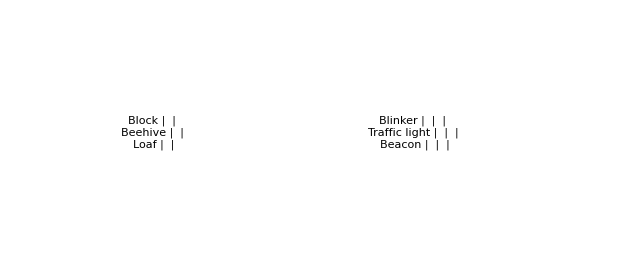

```mathematica
GraphicsRow[{Grid[CellularAutomatonCompositePlot[#,{{"Trails",10,.9}->{Automatic, 60},{"3D",6}->{60, 60}},1]&/@{"Block","Beehive","Loaf"},Dividers->{False,All},FrameStyle->Opacity[.3 ], Spacings->{2->2.5, 2.5}], Grid[CellularAutomatonCompositePlot[#,{"Static"->{60, 60},{"Trails",10,.9}->{60, 60},{"3D",6}->{60, 60}},1]&/@{"Blinker","Traffic light","Beacon"},Dividers->{False,All},FrameStyle->Opacity[.3 ], Spacings->{{4, {2-> 5, 3->5}}, 2.5}]}, Spacings->{40, Automatic}]
```

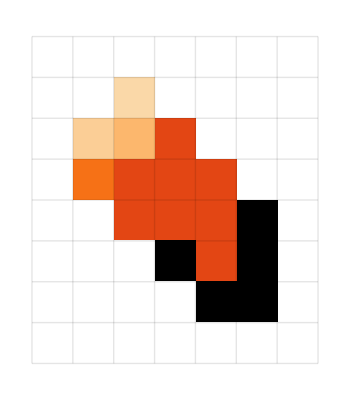
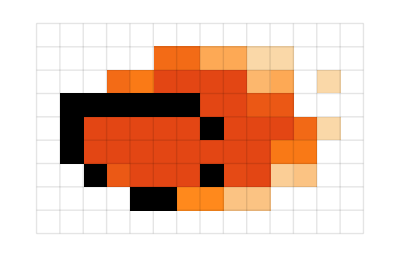
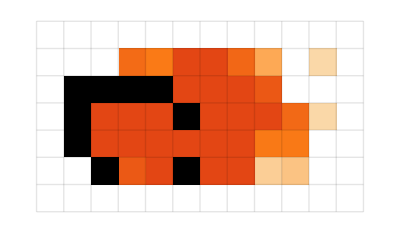
Glider | -Graphics- | -Graphics- | -Graphics3D-
Heavyweight spaceship | -Graphics- | -Graphics- | -Graphics3D-
Lightweight spaceship | -Graphics- | -Graphics- | -Graphics3D-

```mathematica
Grid[CellularAutomatonCompositePlot[#,{"Static"->{75, 75}, {"Trails",10,.9}->{Automatic, 75},{"3D",6}->{75, 75}},1]&/@{"Glider","Heavyweight spaceship","Lightweight spaceship"},Dividers->{False,All},FrameStyle->Opacity[.3 ], Spacings->{{4, {2-> 5, 3->5}}, 2.5}]
```

May want to do spacetime plot here, should just drag to adjust graphic sizes because different rows have different plot ranges. 3D Plots are much more illuminating when you run for longer, the gosper glider gun looks fantastic here (once made lighter):

```mathematica
Grid[CellularAutomatonCompositePlot[#,{"Static"->{110, Automatic}, {"Trails",10,.9}->{110, Automatic},{"3D",100}->{110, 110}},1]&/@{"Gosper glider gun","Period-15 glider gun"},Dividers->{False,All},FrameStyle->Opacity[.3 ], Spacings->{{4, 3-> 5}, 2.5}]
```

Gosper glider gun | -Graphics- | -Graphics- | -Graphics3D-
Period-15 glider gun | -Graphics- | -Graphics- | -Graphics3D-

```mathematica
Grid[CellularAutomatonCompositePlot[#,{"Static"->{110, Automatic}, {"Trails",10,.9}->{110, Automatic},{"3D",100}->{110, 110}},1]&/@{"Block-laying switch engine","Noah's ark","Puffer 1","p112 puffer"},Dividers->{False,All},FrameStyle->Opacity[.3 ], Spacings->{{4, 3-> 5}, 2.5}]
```

Block-laying switch engine | -Graphics- | -Graphics- | -Graphics3D-
Noah's ark | -Graphics- | -Graphics- | -Graphics3D-
Puffer 1 | -Graphics- | -Graphics- | -Graphics3D-
p112 puffer | -Graphics- | -Graphics- | -Graphics3D-

See what SW thinks and then we could do more (Using grid because spacings for graphicsgrid are awkward)

```mathematica
Grid[CellularAutomatonCompositePlot[#,{"Static"->{110, Automatic}, {"Trails",10,.9}->{110, Automatic},{"3D",100}->{110, 110}},1]&/@{"Pi ship 1","Flying wing"},Dividers->{False,All},FrameStyle->Opacity[.3 ], Spacings->{{4, 3-> 5}, 2.5}]
```

Pi ship 1 | -Graphics- | -Graphics- | -Graphics3D-
Flying wing | -Graphics- | -Graphics- | -Graphics3D-

Need to add option to control mesh for column 3 here:

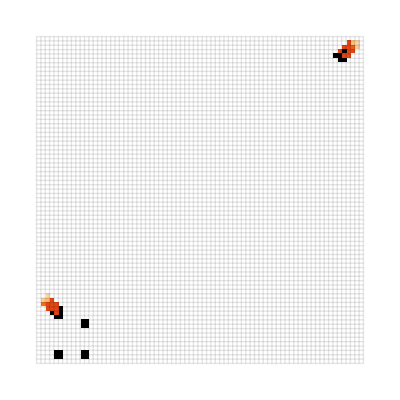
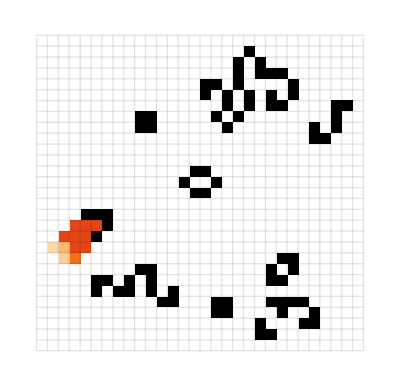
Glider pusher | -Graphics- | -Graphics- | -Graphics3D-
Three-block shifter | -Graphics- | -Graphics- | -Graphics3D-
Snark64 | -Graphics- | -Graphics- | -Graphics3D-

```mathematica
Grid[CellularAutomatonCompositePlot[#,{"StaticNoMesh"->{110, Automatic}, {"Trails",10,.9}->{110, Automatic},{"3D",100}->{110, 110}},1]&/@{"Glider pusher","Three-block shifter","Snark64"},Dividers->{False,All},FrameStyle->Opacity[.3 ], Spacings->{{4, 3-> 5}, 2.5}]
```

```mathematica
Grid[CellularAutomatonCompositePlot[#,{"StaticNoMesh"->{110, Automatic}, {"Trails",10,.9}->{110, Automatic},{"3D",100}->{110, 110}},1]&/@{"RF28B","R64","Conduit 1","G-to-LWSS (2023)"},Dividers->{False,All},FrameStyle->Opacity[.3 ], Spacings->{{4, 3-> 5}, 2.5}]
```

RF28B | -Graphics- | -Graphics- | -Graphics3D-
R64 | -Graphics- | -Graphics- | -Graphics3D-
Conduit 1 | -Graphics- | -Graphics- | -Graphics3D-
G-to-LWSS (2023) | -Graphics- | -Graphics- | -Graphics3D-

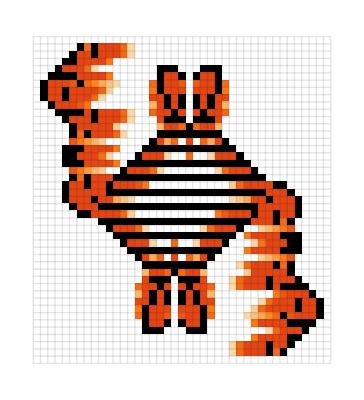
Spacefiller 1 | -Graphics- | -Graphics- | -Graphics3D-

```mathematica
Grid[CellularAutomatonCompositePlot[#,{"StaticNoMesh"->{110, Automatic}, {"Trails",10,.9}->{110, Automatic},{"3D",20}->{110, 110}},1]&/@{"Spacefiller 1"},Dividers->{False,All},FrameStyle->Opacity[.3 ], Spacings->{{4, 3-> 5}, 2.5}]
```

### Make modularity pictures for all the composite guys

```mathematica
ArrayPlot[$LifeData["Gosper glider gun"]["MatrixData"]]
```

-Graphics-

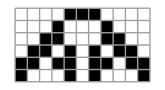
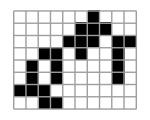
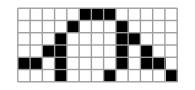
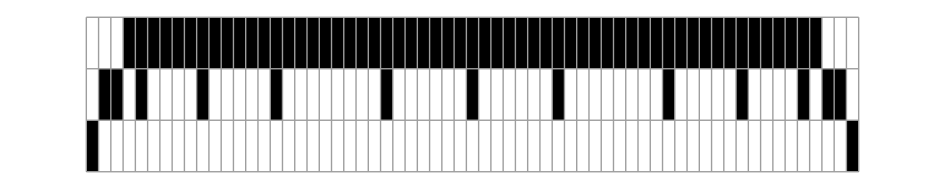
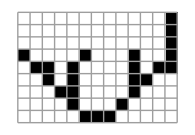
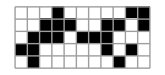
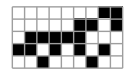
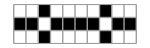
-Graphics-2-Graphics-2-Graphics-1-Graphics-1-Graphics-1-Graphics-1Gosper glider gun
-Graphics-6-Graphics-2-Graphics-2-Graphics-2-Graphics-2-Graphics-1-Graphics-2-Graphics-2-Graphics-2Period-15 glider gun
-Graphics-3-Graphics-1-Graphics-1-Graphics-1Block-laying switch engine
-Graphics-2-Graphics-2-Graphics-2Noah's ark
-Graphics-2-Graphics-2-Graphics-2Puffer 1
-Graphics-3-Graphics-1-Graphics-1-Graphics-1p112 puffer
-Graphics-32-Graphics-26-Graphics-4-Graphics-2-Graphics-2-Graphics-2-Graphics-2-Graphics-2-Graphics-2-Graphics-2-Graphics-1-Graphics-2-Graphics-1Pi ship 1
-Graphics-38-Graphics-34-Graphics-16-Graphics-8-Graphics-4-Graphics-6-Graphics-4-Graphics-2-Graphics-4-Graphics-4-Graphics-2-Graphics-2-Graphics-2-Graphics-2-Graphics-2-Graphics-2-Graphics-1Flying wing
-Graphics-1-Graphics-1-Graphics-1-Graphics-1-Graphics-1Glider pusher
-Graphics-3-Graphics-1-Graphics-1Three-block shifter
-Graphics-2-Graphics-1-Graphics-1-Graphics-1-Graphics-1-Graphics-1-Graphics-1-Graphics-1-Graphics-1Snark64
-Graphics-1-Graphics-1-Graphics-1RF28B
-Graphics-4-Graphics-1-Graphics-1-Graphics-1-Graphics-1R64
-Graphics-1-Graphics-1Conduit 1
-Graphics-2-Graphics-2-Graphics-1-Graphics-1-Graphics-3-Graphics-1-Graphics-2-Graphics-1-Graphics-1G-to-LWSS (2023)
-Graphics-8-Graphics-2-Graphics-2-Graphics-2-Graphics-2-Graphics-4-Graphics-2Spacefiller 1

```mathematica
Column[Labeled[Row[Normal[KeyValueMap[Labeled[ArrayPlot[#, ImageSize->15Last[Dimensions[#]], Mesh->True], #2]&, PatternElements[#MatrixData]&[$LifeData[#]]]], Frame->True], #, Top]&/@{"Gosper glider gun","Period-15 glider gun","Block-laying switch engine","Noah's ark","Puffer 1","p112 puffer","Pi ship 1","Flying wing","Glider pusher","Three-block shifter","Snark64","RF28B","R64","Conduit 1","G-to-LWSS (2023)", "Spacefiller 1"}]
```

#### Over time?


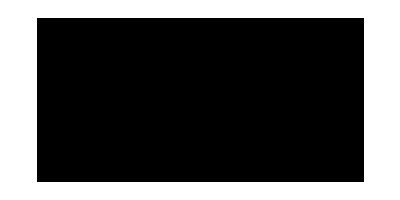
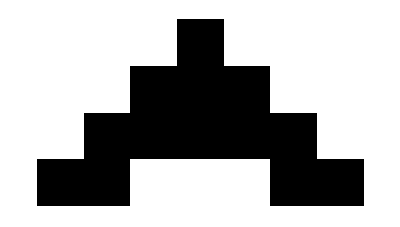
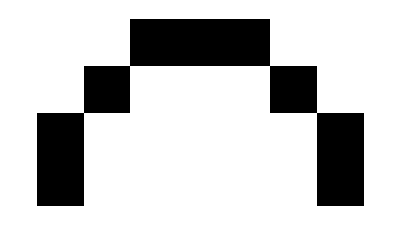
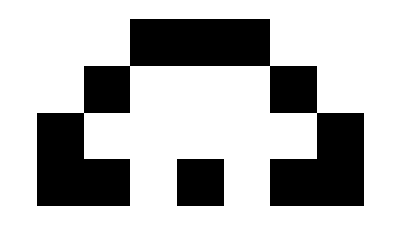
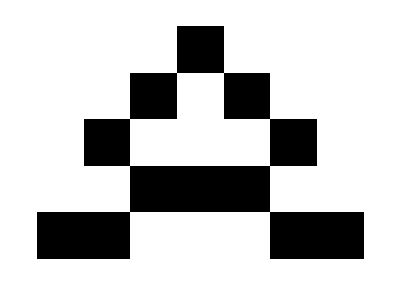
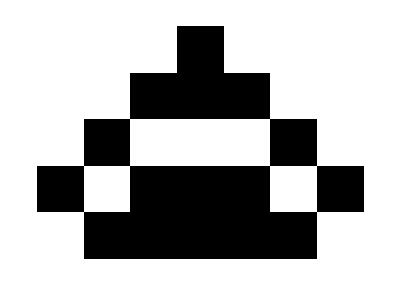
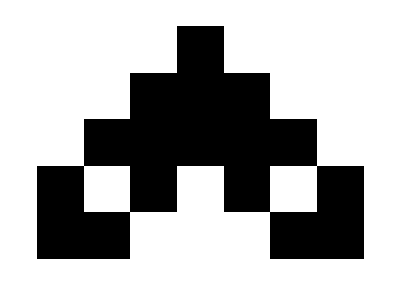
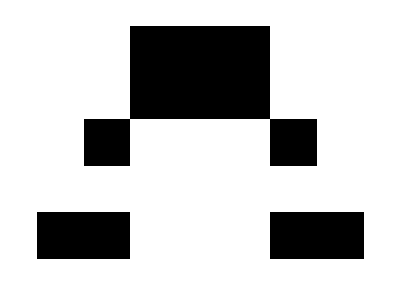
{{-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
Map[ArrayPlot, AllLifeElements[#,$LifeData["Gosper glider gun"]["Period"] ]&/@Keys[PatternElements[#MatrixData]&[$LifeData["Gosper glider gun"]]], {2}]
```

I’m confused what the hell this is even doing^. How do I get all the individual components over time

### Bounding box of composite guys

```mathematica
ParallelMap[BoundingBoxLayeredGraph[$LifeData[#]]&,{"Gosper glider gun","Period-15 glider gun","Block-laying switch engine","Noah's ark","Puffer 1","p112 puffer","Pi ship 1","Flying wing","Glider pusher","Three-block shifter","Snark64","RF28B","R64","Conduit 1","G-to-LWSS (2023)", "Spacefiller 1"}]
```

$Aborted

```mathematica
$LifeData[#]["Period"]&/@{"Gosper glider gun","Period-15 glider gun","Block-laying switch engine","Noah's ark","Puffer 1","p112 puffer","Pi ship 1","Flying wing","Glider pusher","Three-block shifter","Snark64","RF28B","R64","Conduit 1","G-to-LWSS (2023)", "Spacefiller 1"}
```

{30,15,288,1344,128,112,Missing[KeyAbsent,Period],Missing[KeyAbsent,Period],30,Missing[KeyAbsent,Period],Missing[KeyAbsent,Period],Missing[KeyAbsent,Period],Missing[KeyAbsent,Period],Missing[KeyAbsent,Period],Missing[KeyAbsent,Period],Missing[KeyAbsent,Period]}

```mathematica
BoundingBoxLayeredGraph/@Select[$LifeData[#]&/@{"Gosper glider gun","Period-15 glider gun","Block-laying switch engine","Noah's ark","Puffer 1","p112 puffer","Pi ship 1","Flying wing","Glider pusher","Three-block shifter","Snark64","RF28B","R64","Conduit 1","G-to-LWSS (2023)", "Spacefiller 1"}, KeyExistsQ[#, "Period"]&&#[["Period"]] <= 300&][[;;3]]
```

$Aborted

### Trying to understand LifeClosure

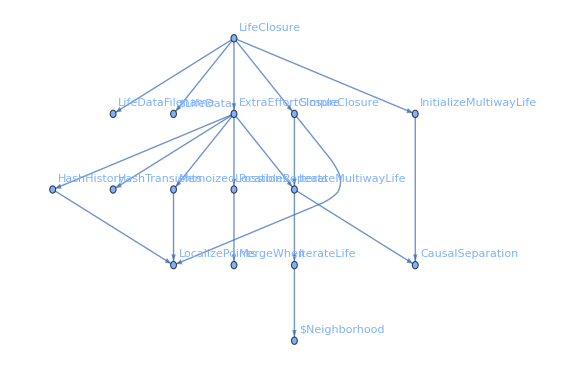

```mathematica
ResourceFunction["SymbolDependencyGraph"][LifeClosure,VertexLabels->Automatic]
```

```mathematica
LifeClosure[state_?MatrixQ,max_Integer:5000,
opts:OptionsPattern[{"Class"->None}]
]:=With[{init=InitializeMultiwayLife[state]},
Switch[OptionValue["Class"],
Alternatives["Oscillator","Spaceship",
"Strict still life","Induction coil"],
SimpleClosure[init,max],
_,
ExtraEffortClosure[init,max]
]
]
```

```mathematica
LifeClosure[$LifeData["Period-15 glider gun"]["MatrixData"]]
```

```mathematica
InitializeMultiwayLife[$LifeData["Period-15 glider gun"]["MatrixData"]]
```

<|1→<|Data→{{10,26},{11,25},{11,27},{12,26},{13,22},{13,23},{14,21},{14,22},{14,23},{15,21},{15,22},{15,25},{15,26},{16,20},{16,21},{16,26},{17,20},{17,22},{17,24},{17,25},{17,26},{18,21},{18,24},{19,24},{19,25},{19,26},{20,25},{20,27},{21,23},{21,26},{21,28},{22,23},{22,27},{22,28},{23,23}},InComponents→{}|>,2→<|Data→{{2,8},{3,3},{3,4},{3,8},{4,3},{4,5},{4,8},{5,4},{5,6},{6,5},{6,6},{6,7},{7,7},{7,10},{8,5},{8,6},{8,7},{8,9},{8,11},{9,5},{9,10},{9,11},{10,5},{10,6},{10,9},{10,10},{11,8},{11,9},{11,10},{12,8},{12,9},{13,5},{14,4},{14,6},{15,5}},InComponents→{}|>,3→<|Data→{{20,2},{20,3},{20,5},{20,6},{20,8},{20,9},{21,2},{21,3},{21,8},{21,9},{22,2},{22,3},{22,5},{22,6},{22,8},{22,9},{24,5},{24,6},{25,3},{25,8},{26,2},{26,9},{27,1},{27,10},{28,1},{28,10},{29,1},{29,10},{30,2},{30,9},{31,3},{31,8},{32,5},{32,6}},InComponents→{}|>,4→<|Data→{{9,15},{9,16},{10,15},{10,16},{10,17},{10,19},{11,16},{11,19},{12,16},{12,17},{13,14},{13,15},{14,12},{14,15},{15,12},{15,14},{15,15},{15,16},{16,15},{16,16}},InComponents→{}|>,5→<|Data→{{1,22},{2,20},{2,21},{2,22},{3,19},{4,19},{4,20}},InComponents→{}|>,6→<|Data→{{1,12},{2,12},{2,13},{2,14},{3,15},{4,14},{4,15}},InComponents→{}|>|>

```mathematica
frames=Position[Transpose[
Reverse[Normal[$LifeData["Period-15 glider gun"]["MatrixData"]]]],1]
```

{{1,12},{1,22},{2,8},{2,12},{2,13},{2,14},{2,20},{2,21},{2,22},{3,3},{3,4},{3,8},{3,15},{3,19},{4,3},{4,5},{4,8},{4,14},{4,15},{4,19},{4,20},{5,4},{5,6},{6,5},{6,6},{6,7},{7,7},{7,10},{8,5},{8,6},{8,7},{8,9},{8,11},{9,5},{9,10},{9,11},{9,15},{9,16},{10,5},{10,6},{10,9},{10,10},{10,15},{10,16},{10,17},{10,19},{10,26},{11,8},{11,9},{11,10},{11,16},{11,19},{11,25},{11,27},{12,8},{12,9},{12,16},{12,17},{12,26},{13,5},{13,14},{13,15},{13,22},{13,23},{14,4},{14,6},{14,12},{14,15},{14,21},{14,22},{14,23},{15,5},{15,12},{15,14},{15,15},{15,16},{15,21},{15,22},{15,25},{15,26},{16,15},{16,16},{16,20},{16,21},{16,26},{17,20},{17,22},{17,24},{17,25},{17,26},{18,21},{18,24},{19,24},{19,25},{19,26},{20,2},{20,3},{20,5},{20,6},{20,8},{20,9},{20,25},{20,27},{21,2},{21,3},{21,8},{21,9},{21,23},{21,26},{21,28},{22,2},{22,3},{22,5},{22,6},{22,8},{22,9},{22,23},{22,27},{22,28},{23,23},{24,5},{24,6},{25,3},{25,8},{26,2},{26,9},{27,1},{27,10},{28,1},{28,10},{29,1},{29,10},{30,2},{30,9},{31,3},{31,8},{32,5},{32,6}}

So Causal separation is just doing the morphologicalcomponents thing:

```mathematica
CausalSeparation[framePts_]:=Map[
Union,WeaklyConnectedComponents[
NearestNeighborGraph[framePts,
{All,2Sqrt[2]}]]]
```

And iterate multiway life just does this repeatedly does this

Now SimpleClosure, does lifeclosure but it takes a t-value, so I switched these functions to simple closure and now it takes a t value:

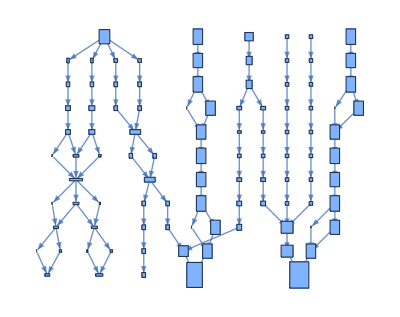

```mathematica
BoundingBoxLayeredGraph[$LifeData["Period-15 glider gun"], 10]
```

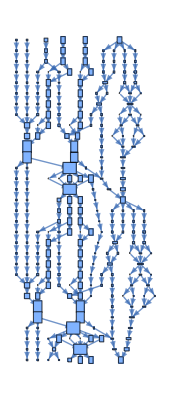

```mathematica
BoundingBoxLayeredGraph[$LifeData["Period-15 glider gun"], 30]
```

### Now another potential way to visualize dependency is to look at the graph intersection of different components

#### V1

```mathematica
Union@Values[$LifeData][[All, "Class"]]
```

{Agar,Breeder,Caber tosser,Conduit,Constellation,Crawler,Eater,Fuse,Growing spaceship,Gun,Induction coil,Memory cell,Methuselah,Oscillator,Problem,Pseudo still life,Puffer,Reflector,Rotor,Sawtooth,Spacefiller,Spaceship,Spark,Still life component,Strict still life,Superstring,Unit cell,Wave,Wick,Wickstretcher}

```mathematica
allmultis = 
ParallelMap[
LifeMultiwayGraph[LifeClosure[#MatrixData, 100]]&, Values[$LifeData]
];
```

$Aborted

```mathematica
Join[<|a->1|>, <|b->1|>]
```

<|a→1,b→1|>

```mathematica
all = Join[Sequence@@Values[$LifeParts]];
```

```mathematica
mat=Boole[Outer[SubsetQ[#2,#1]&,
Values[all],
Values[all],
1]];
```

```mathematica
overlap = Select[Position[mat, 1], #[[1]] != #[[2]]&];
```

```mathematica
names = Map[Keys[all][[#]]&, overlap, {2}];
```

```mathematica
years = Map[$LifeData[#]["Year"]&, names, {2}];
```

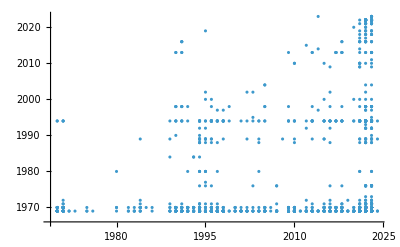

```mathematica
ListPlot[Reverse/@years]
```

```mathematica
ArrayPlot[#MatrixData]&/@Map[$LifeData[#]&, names, {2}][[1]]
```

{-Graphics-,-Graphics-}

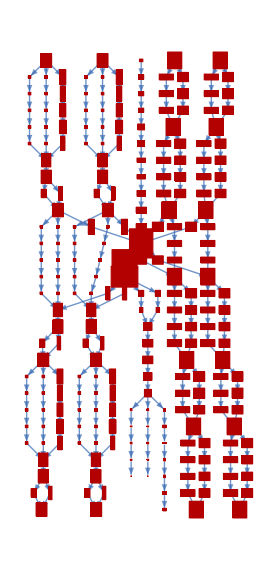

```mathematica
With[{g = BoundingBoxLayeredGraph[#2]}, HighlightGraph[g, GraphIntersection[g,BoundingBoxLayeredGraph[#1]]]]&@@@ Map[$LifeData[#]&, names, {2}][[;;1]]
```

```mathematica
{PatternsLayeredGraph[#1], PatternsLayeredGraph[#2]}&@@@ Map[$LifeData[#]&, names, {2}][[;;1]]
```

```mathematica
i = With[{g = BoundingBoxLayeredGraph[#2]}, {VertexList[g], VertexList[BoundingBoxLayeredGraph[#2]]}]&@@@ Map[$LifeData[#]&, names, {2}][[;;1]];
```

```mathematica
i = {BoundingBoxLayeredGraph[#1], BoundingBoxLayeredGraph[#2]}&@@@ Map[$LifeData[#]&, names, {2}][[;;1]];
```

```mathematica
i = {BoundingBoxLayeredGraph[#1], BoundingBoxLayeredGraph[#2]}&@@@ Map[$LifeData[#]&, names, {2}][[;;1]];
```

```mathematica
vs = Map[VertexList, i, {2}];
```

```mathematica
cs = Map[VertexCount, i, {2}];
```

```mathematica
vs[[1, 2]]
```

```mathematica
i[[1, 2, 2]]
```

{1,2,{{1,15},{1,17},{1,18},{1,23},{1,24},{1,26},{2,15},{2,16},{2,19},{2,22},{2,25},{2,26},{3,13},{3,14},{3,18},{3,23},{3,27},{3,28},{4,12},{4,16},{4,17},{4,19},{4,20},{4,21},{4,22},{4,24},{4,25},{4,29},{5,13},{5,14},{5,15},{5,17},{5,19},{5,22},{5,24},{5,26},{5,27},{5,28},{6,15},{6,17},{6,19},{6,22},{6,24},{6,26},{7,18},{7,23},{8,19},{8,22},{9,19},{9,22},{11,16},{11,17},{11,24},{11,25},{12,16},{12,25},{13,17},{13,18},{13,23},{13,24},{14,19},{14,22},{15,15},{15,16},{15,17},{15,18},{15,19},{15,20},{15,21},{15,22},{15,23},{15,24},{15,25},{15,26},{16,14},{16,27},{17,15},{17,16},{17,17},{17,18},{17,23},{17,24},{17,25},{17,26},{19,15},{19,16},{19,17},{19,24},{19,25},{19,26},{20,14},{20,17},{20,24},{20,27},{21,14},{21,15},{21,18},{21,19},{21,20},{21,21},{21,22},{21,23},{21,26},{21,27}}}

```mathematica
i[[1,1, 1]]
```

{1,1,{{36,19},{36,20},{36,23},{36,24},{36,25},{36,26},{36,27},{36,28},{36,31},{36,32},{37,19},{37,22},{37,29},{37,32},{38,20},{38,21},{38,22},{38,29},{38,30},{38,31},{40,20},{40,21},{40,22},{40,23},{40,28},{40,29},{40,30},{40,31},{41,19},{41,32},{42,20},{42,21},{42,22},{42,23},{42,24},{42,25},{42,26},{42,27},{42,28},{42,29},{42,30},{42,31},{43,24},{43,27},{44,22},{44,23},{44,28},{44,29},{45,21},{45,30},{46,21},{46,22},{46,29},{46,30},{48,24},{48,27},{49,24},{49,27},{50,23},{50,28},{51,20},{51,22},{51,24},{51,27},{51,29},{51,31},{52,18},{52,19},{52,20},{52,22},{52,24},{52,27},{52,29},{52,31},{52,32},{52,33},{53,17},{53,21},{53,22},{53,24},{53,25},{53,26},{53,27},{53,29},{53,30},{53,34},{54,18},{54,19},{54,23},{54,28},{54,32},{54,33},{55,20},{55,21},{55,24},{55,27},{55,30},{55,31},{56,20},{56,22},{56,23},{56,28},{56,29},{56,31}}}

```mathematica
i[[1, -1]]  // Length
```

252

```mathematica
sas = Map[SparseArray[
Thread[
(Transpose[{#[[All, 1]] -  Min[#[[All, 1]]]+1, #[[All, 2]] -  Min[#[[All, 2]]]+1}]&[
Ramp[#[[-1]] ]]+ 1)->1]]&, vs, {3}];
```

```mathematica
sis = Intersection@@@sas;
```

```mathematica
Length[sas[[1, 1]]]
```

18

```mathematica
VertexCount
```

```mathematica
Length[sas[[1, 2]]]
```

252

```mathematica
Intersection[SparseArray[i[[1, 1, -1]], i[[1, -1]]]
```

```mathematica
overlap[[1]]
```

{2,397}

```mathematica
Keys[all][[2]]
```

104P9

```mathematica
Keys[all][[397]]
```

p27lumpsofmuckhassler

```mathematica
RandomSample[overlap, 3]
```

{{885,305},{1125,1138},{212,600}}

#### V2

```mathematica
names[[1]]
```

{104P9,p27lumpsofmuckhassler}

```mathematica
{PatternsLayeredGraph[#1], PatternsLayeredGraph[#2]}&@@@ Map[$LifeData[#]&, names, {2}][[;;1]]
```

```mathematica
With[{g = PatternsLayeredGraph[#2]}, (*HighlightGraph[g, *)VertexList[GraphIntersection[g,PatternsLayeredGraph[#1]]]]&@@@ Map[$LifeData[#]&, names, {2}][[;;1]]
```

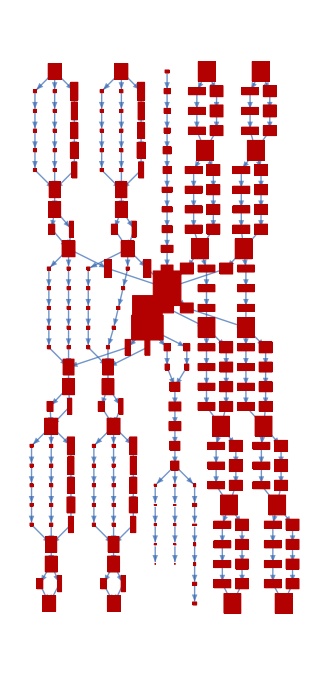

```mathematica
With[{g = BoundingBoxLayeredGraph[#2]}, HighlightGraph[g, GraphIntersection[g,BoundingBoxLayeredGraph[#1]]]]&@@@ Map[$LifeData[#]&, names, {2}][[;;1]]
```

```mathematica
With[{g = BoundingBoxLayeredGraph[#2]}, Length[VertexList[GraphIntersection[g,BoundingBoxLayeredGraph[#1]]]]]&@@@ Map[$LifeData[#]&, names, {2}][[;;1]]
```

{270}

```mathematica
aps = (Map[ArrayPlot[SparseArray[
Thread[
(Transpose[{#[[All, 1]] -  Min[#[[All, 1]]]+1, #[[All, 2]] -  Min[#[[All, 2]]]+1}]&[
Ramp[#[[-1]] ]]+ 1)->1]], ImageSize->Tiny]&, VertexList/@ gs, {2}]);
```

```mathematica
aps[[1]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Intersection@@aps
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
sas = Map[SparseArray[
Thread[
(Transpose[{#[[All, 1]] -  Min[#[[All, 1]]]+1, #[[All, 2]] -  Min[#[[All, 2]]]+1}]&[
Ramp[#[[-1]] ]]+ 1)->1]]&, vs, {3}]
```

```mathematica
Intersection@@(Catenate[Last[#]]&/@(VertexList/@ gs))
```

Catenate::invrp: The argument 10 is not a valid Association or a list.

Catenate::invrp: The argument 28 is not a valid Association or a list.

Catenate::argx: Catenate called with 0 arguments; 1 argument is expected.

Catenate[]

```mathematica
sas = (Map[SparseArray[
Thread[
(Transpose[{#[[All, 1]] -  Min[#[[All, 1]]]+1, #[[All, 2]] -  Min[#[[All, 2]]]+1}]&[
Ramp[#[[-1]] ]]+ 1)->1]]&, VertexList/@ gs, {2}]);
```

```mathematica
commonElements=Intersection[list1,list2]; (*Find common elements*)

positions1=Flatten[Position[list1,#]]&/@commonElements;
positions2=Flatten[Position[list2,#]]&/@commonElements;

Transpose[{commonElements,positions1,positions2}]
```

```mathematica
$LifeData["Pi ship 1"]
```

<|Name→Pi ship 1,Year→1971,Class→Growing spaceship,Wiki→https://conwaylife.com/wiki/Pi_ship_1,DataFiles→{piship1.cells,piship1.rle},MatrixData→SparseArray[Automatic,{29,99},0,{1,{{0,2,8,30,50,90,134,186,212,212,254,258,321,352,372,404,414,426,426,430,434,434,434,434,434,435,438,440,448,452},{{8},{92},{7},{8},{9},{91},{92},{93},{5},{6},{8},{9},{10},{31},{32},{33},{43},{44},{45},{55},{56},{57},{67},{68},{69},{90},{91},{92},{94},{95},{6},{9},{11},{12},{17},{22},{30},{34},{42},{46},{54},{58},{66},{70},{78},{83},{88},{89},{91},{94},{3},{4},{6},{11},{13},{15},{16},{18},{19},{21},{22},{23},{29},{30},{34},{35},{41},{42},{46},{47},{53},{54},{58},{59},{65},{66},{70},{71},{77},{78},{79},{81},{82},{84},{85},{87},{89},{94},{96},{97},{3},{4},{6},{8},{11},{13},{21},{22},{23},{24},{28},{29},{31},{33},{35},{36},{40},{41},{43},{45},{47},{48},{52},{53},{55},{57},{59},{60},{64},{65},{67},{69},{71},{72},{76},{77},{78},{79},{87},{89},{92},{94},{96},{97},{3},{12},{13},{14},{16},{18},{20},{21},{24},{25},{27},{28},{30},{31},{33},{34},{36},{37},{39},{40},{42},{43},{45},{46},{48},{49},{51},{52},{54},{55},{57},{58},{60},{61},{63},{64},{66},{67},{69},{70},{72},{73},{75},{76},{79},{80},{82},{84},{86},{87},{88},{97},{2},{3},{11},{12},{25},{27},{31},{33},{37},{39},{43},{45},{49},{51},{55},{57},{61},{63},{67},{69},{73},{75},{88},{89},{97},{98},{6},{7},{8},{24},{25},{27},{28},{30},{31},{33},{34},{36},{37},{39},{40},{42},{43},{45},{46},{48},{49},{51},{52},{54},{55},{57},{58},{60},{61},{63},{64},{66},{67},{69},{70},{72},{73},{75},{76},{92},{93},{94},{5},{9},{91},{95},{4},{5},{10},{22},{23},{24},{25},{26},{27},{28},{29},{30},{31},{32},{33},{34},{35},{36},{37},{38},{39},{40},{41},{42},{43},{44},{45},{46},{47},{48},{49},{50},{51},{52},{53},{54},{55},{56},{57},{58},{59},{60},{61},{62},{63},{64},{65},{66},{67},{68},{69},{70},{71},{72},{73},{74},{75},{76},{77},{78},{90},{95},{96},{3},{5},{7},{8},{10},{11},{15},{16},{17},{20},{21},{23},{28},{34},{43},{50},{57},{66},{72},{77},{79},{80},{83},{84},{85},{89},{90},{92},{93},{95},{97},{2},{3},{5},{10},{12},{13},{15},{16},{17},{19},{81},{83},{84},{85},{87},{88},{90},{95},{97},{98},{1},{6},{10},{15},{17},{22},{27},{29},{31},{33},{35},{42},{44},{46},{47},{49},{51},{53},{54},{56},{58},{65},{67},{69},{71},{73},{78},{83},{85},{90},{94},{99},{13},{19},{20},{37},{40},{60},{63},{80},{81},{87},{1},{2},{10},{11},{37},{40},{60},{63},{89},{90},{98},{99},{37},{40},{60},{63},{38},{39},{61},{62},{50},{49},{50},{51},{48},{52},{38},{39},{48},{49},{51},{52},{61},{62},{38},{39},{61},{62}}},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}],InitialWeight→452|>

```mathematica
Function[{left, right}, With[{common=Intersection[left,right]},Transpose[{Flatten[Position[left,#]]&/@common,Flatten[Position[right,#]]&/@common}]]]@@sas
```

{{{4},{35,109,190}},{{6},{55,129,217}},{{8},{60,135,224}},{{10},{67,141,233}},{{15},{13,94,169}},{{2,17},{24,102,180}},{{12},{74,148,240}},{{13},{76,150,242}},{{3},{37,111,192}},{{11},{69,143,235}},{{9},{62,137,226}},{{7},{57,131,219}},{{16},{15,96,171}},{{1,18},{26,182}},{{5},{46,119,206}},{{14},{2,85,160,251}}}

```mathematica
Function[{left, right},With[{common=Intersection[left,right]},Flatten[Position[left,#]]&/@common->Flatten[Position[right,#]]&/@common]]@@sas
```

{{{4},{6},{8},{10},{15},{2,17},{12},{13},{3},{11},{9},{7},{16},{1,18},{5},{14}}→{35,109,190},{{4},{6},{8},{10},{15},{2,17},{12},{13},{3},{11},{9},{7},{16},{1,18},{5},{14}}→{55,129,217},{{4},{6},{8},{10},{15},{2,17},{12},{13},{3},{11},{9},{7},{16},{1,18},{5},{14}}→{60,135,224},{{4},{6},{8},{10},{15},{2,17},{12},{13},{3},{11},{9},{7},{16},{1,18},{5},{14}}→{67,141,233},{{4},{6},{8},{10},{15},{2,17},{12},{13},{3},{11},{9},{7},{16},{1,18},{5},{14}}→{13,94,169},{{4},{6},{8},{10},{15},{2,17},{12},{13},{3},{11},{9},{7},{16},{1,18},{5},{14}}→{24,102,180},{{4},{6},{8},{10},{15},{2,17},{12},{13},{3},{11},{9},{7},{16},{1,18},{5},{14}}→{74,148,240},{{4},{6},{8},{10},{15},{2,17},{12},{13},{3},{11},{9},{7},{16},{1,18},{5},{14}}→{76,150,242},{{4},{6},{8},{10},{15},{2,17},{12},{13},{3},{11},{9},{7},{16},{1,18},{5},{14}}→{37,111,192},{{4},{6},{8},{10},{15},{2,17},{12},{13},{3},{11},{9},{7},{16},{1,18},{5},{14}}→{69,143,235},{{4},{6},{8},{10},{15},{2,17},{12},{13},{3},{11},{9},{7},{16},{1,18},{5},{14}}→{62,137,226},{{4},{6},{8},{10},{15},{2,17},{12},{13},{3},{11},{9},{7},{16},{1,18},{5},{14}}→{57,131,219},{{4},{6},{8},{10},{15},{2,17},{12},{13},{3},{11},{9},{7},{16},{1,18},{5},{14}}→{15,96,171},{{4},{6},{8},{10},{15},{2,17},{12},{13},{3},{11},{9},{7},{16},{1,18},{5},{14}}→{26,182},{{4},{6},{8},{10},{15},{2,17},{12},{13},{3},{11},{9},{7},{16},{1,18},{5},{14}}→{46,119,206},{{4},{6},{8},{10},{15},{2,17},{12},{13},{3},{11},{9},{7},{16},{1,18},{5},{14}}→{2,85,160,251}}

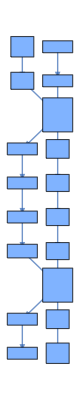
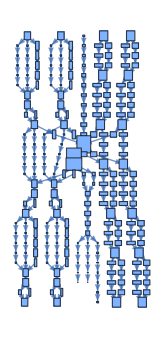

```mathematica
(BoundingBoxLayeredGraph/@ Map[$LifeData[#]&, names, {2}][[1]])
```

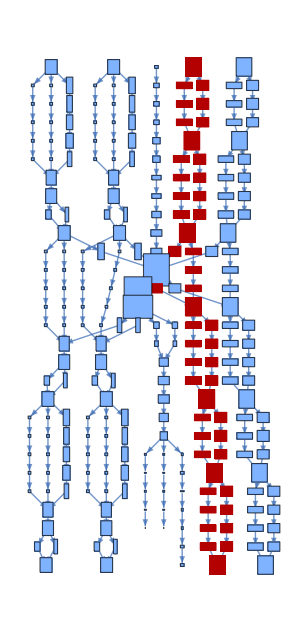

```mathematica
HighlightGraph[#[[2]], 
VertexList[#[[2]]][[
(Function[{left, right},With[{common=Intersection[left,right]},{Flatten[Position[left,#]&/@common],Flatten[Position[right,#]&/@common]}]]@@
(Map[
(SparseArray[
Thread[
(Transpose[{#[[All, 1]] -  Min[#[[All, 1]]]+1, #[[All, 2]] -  Min[#[[All, 2]]]+1}]&[
Ramp[#[[-1]] ]]+ 1)->1]]&), 
VertexList/@ #, {2}]))[[2]]]]]&@ (BoundingBoxLayeredGraph/@ Map[$LifeData[#]&, names, {2}][[1]])
```